# 26: Hessenberg Reduction:

```mathematica
SetOptions[MatrixPlot,ColorRules->{0->Green}];
```

We know the standard way to do QR.  Work your way through the columns of the matrix choosing v according to the fairly simple recipe in lecture 10 and make zeros using the Householder reflection H=I-2v⊗v until you run out of columns! The reason for doing this was to reduce A.x=b to a simpler triangular form.

In a very similar way we are going systematically make zeros using Householder reflections in a similarity transformation
	A→Q.A.Qᵀ=H	
that preserve eigenvalues.  The reason for doing this is to reduce A to a simpler form: eventually one that just lets you read the eigenvalues from the diagonal!

## Optimistic Attempt

The plan is to make zeros in a matrix while not changing the eigenvalues!  To preserve the eigenvalues we need to use a similarity transformation
	A⟶Y.A.Y^-1
Since we are going to do a lot of matrix operations it is crucial that we use orthogonal similarity transformations
	A⟶Q.A.Qᵀ.
As an experiment we will see what happens if we try to zero an entire column and leave only the top element like we did before using our householder Q. Since the Householder Q is symmetric the Qᵀ=Q on the right does the same operations on the columns as Q on the left does on the rows.  As a result, similarity transformation destroys the zeros that were created in Q.A.

```mathematica
m=6;
A=RandomReal[{-1,1},{m,m}];
a1=A⟦All,1⟧;
Q=HouseMat[a1];
QA=Q.A; QAQtr=QA.Q;
TabView[{
"Q.A"->MatrixPlot[Chop[QA]],
"Q.A.Qᵀ"->MatrixPlot[Chop[QAQtr]]}]
```

12

This does not make zeros! It does however “usually” make matrices more Upper Triangular. The norm of strictly lower triangular portion divided by the norm of the entire thing is a reasonable way to measure degree of UTness!  We are going to use the Frobenius norm and note that since H is orthogonal the norm is unchanged by the similarity transformation!

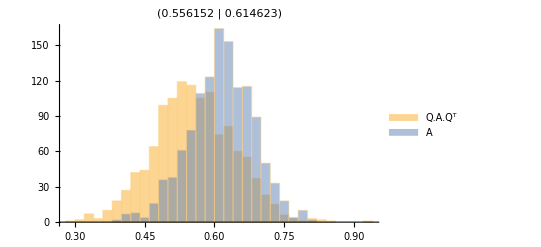

```mathematica
m=6;
SampleSize=1234;
Data=Table[
A=RandomReal[{-1,1},{m,m}];
a1=A⟦All,1⟧;
Q=HouseMat[a1];
QA=Q.A; QAQtr=QA.Qᵀ;
Map[Norm[LowerTriangularize[#,-1],"Frobenius"]&,{QAQtr,A}],
{SampleSize}]/Norm[A,"Frobenius"];
Histogram[Dataᵀ,20,ChartLegends->{"Q.A.Qᵀ","A"},PlotLabel->{Map[Mean,Dataᵀ]}]
```

We will come back to this!  For right now we want to make zeros that stay zeros!

## Realistic Attempt: Hessenberg Decomposition

The plan is to make zeros in a matrix while not changing the eigenvalues!  To preserve the eigenvalues we need to use a similarity transformation
	A⟶Y.A.Y^-1
Since we are going to do a lot of matrix operations it is crucial that we use orthogonal similarity transformations
	A⟶Q.A.Qᵀ.
As we saw zeroing the whole column (except the top element) is too greedy. However, if we try to zero everything except the top two elements we get zeros that are preserved.

This goes something like this.  Note that the H on the right makes zeros in the first column using rows 2 and above. It does not touch the first row! As a result, the Hᵀ=H on the left does not touch the first column and preserves the zeros that were just introduced!

```mathematica
m=6;
A=RandomReal[{-1,1},{m,m}];
a1=A⟦All,1⟧;
v=Join[{0},HouseVec[a1⟦2;;-1⟧]];
Q=IdentityMatrix[m]-2 KroneckerProduct[v,v];
QA=Q.A; QAQtr=QA.Qᵀ;
TabView[{
"Q"->MatrixPlot[Chop[Q]],
"Q.A"->MatrixPlot[Chop[QA]],
"Q.A.Qᵀ"->MatrixPlot[Chop[QAQtr]]}]
```

123

Sweeping down the columns in a loop produces an almost upper triangular matrix with a single lower diagonal.  Accumulating these reflections into a single orthogonal matrix Q gives a decomposition
	A=Q.H.Qᵀ
where the inner matrix is upper triangular with one extra non-zero lower diagonal.  The inner matrix is called a Hessenberg matrix.

The eigenvalues of H are the same as the eigenvalues of A.  You do not build the orthogonal Q unless you need the eigenvectors.  in fact, you never need to build the Householder matrices.  This is a Mathematica implementation of algorithm 26.1.

```mathematica
Algorithm26Point1[AIn_]:= Module[{A=AIn, m=Length[AIn],v,x},
Do[
x=A⟦k+1;;m,k⟧;
v=x; v⟦1⟧=v⟦1⟧+Sign[x⟦1⟧]*Norm[x]; (* standard least cancellation choice *)
v=Normalize[v];
A⟦k+1;;m,k;;m⟧=A⟦k+1;;m,k;;m⟧-2 KroneckerProduct[v,v.A⟦k+1;;m,k;;m⟧];
A⟦1;;m,k+1;;m⟧=A⟦1;;m,k+1;;m⟧-2 KroneckerProduct[A⟦1;;m,k+1;;m⟧.v,v],
{k,1,m-2}];
Chop[A]
]
```

This is a modification which always gives positive entries on the sub diagonal.  We do not really need this but it gives us a uniqueness theorem for Hessenberg reductions.

```mathematica
HessenbergReduction[AIn_]:= Module[{A=AIn, m=Length[AIn],v,x},
Do[
x=A⟦k+1;;m,k⟧;
v=x; v⟦1⟧=v⟦1⟧-Norm[x];(* positive on subdiagonal choice *)
v=Normalize[v];
A⟦k+1;;m,k;;m⟧=A⟦k+1;;m,k;;m⟧-2 KroneckerProduct[v,v.A⟦k+1;;m,k;;m⟧];
A⟦1;;m,k+1;;m⟧=A⟦1;;m,k+1;;m⟧-2 KroneckerProduct[A⟦1;;m,k+1;;m⟧.v,v],
{k,1,m-2}];
Chop[A]]
```

As always test.

5.66802×10^-15

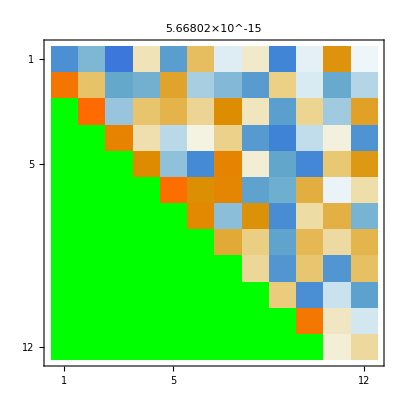

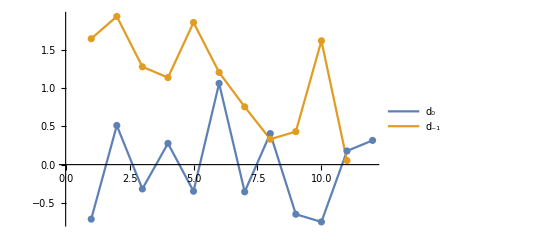

```mathematica
m=12;
A=RandomReal[{-1,1},{m,m}];
H=HessenbergReduction[A];
{λA,λH}=Map[Eigenvalues,{A,H}];
Norm[λA-λH]
TableForm[{λA,λH}];
MatrixPlot[H,PlotLabel->Norm[λA-λH]]
ListPlot[{Diagonal[H,0],Diagonal[H,-1]},
Joined->True,Mesh->All, PlotLegends->{"d_0","d_-1"}]
```

If Q is needed as well we can accumulate the Q just like in the QR algorithm.  Every linear algebra tool has a Hessenberg command.   In Mathematica the command is HessenbergDecomposition which gives H and Q.

## Symmetric Hessenberg Decomposition

The question is what happens if we run the Hessenberg decomposition on a symmetric matrix. Since all the operations preserve symmetry we get a Symmetric tri-diagonal matrix which can be stored as two vectors!

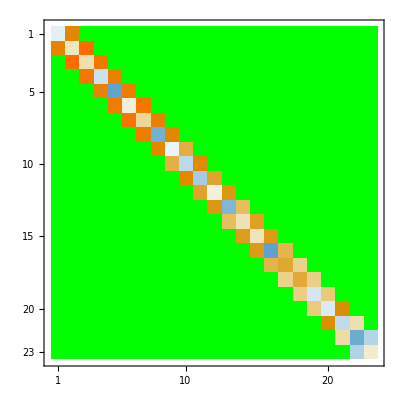

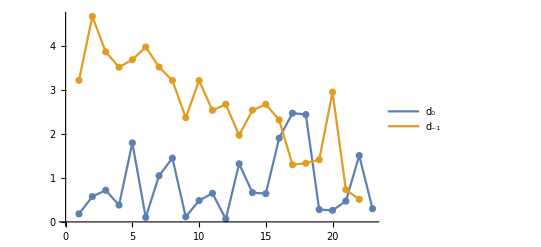

```mathematica
m=23;
S=RandomReal[{-1,1},{m,m}];S=S+Sᵀ;
T = Chop[HessenbergReduction[S]];
MatrixPlot[T]
ListPlot[Abs[{Diagonal[T,0],Diagonal[T,-1]}],
Joined->True,Mesh->All, PlotLegends->{"d_0","d_-1"}]
```

## Hessenberg Decomposition Commands

The Hessenberg command in Mathematica returns Q and H.  With H=Qᵀ.A.Q.  It does not give positive sub diagonals!

```mathematica
m=23;
A=RandomComplex[{-1-I,1+I},{m,m}];
{Q,H}=HessenbergDecomposition[A];
QhQ=Chop[ConjugateTranspose[Q].Q];
QhAQ=Chop[ConjugateTranspose[Q].A.Q];

TabView[{
"Q^H.Q"->MatrixPlot[QhQ],
"H=Q^H.A.Q"->MatrixPlot[QhAQ],
"subdia(H)"->ListPlot[Diagonal[QhAQ,-1],PlotRange->All]
}]
```

123

## Hessenberg Uniqueness

### QR Decomposition Uniqueness Theorem

Remember, although QR decompositions are not unique and there are a variety of different algorithms (GS, MGS, Householder) to compute them. The QR decomposition is almost unique in the sense that the only choices are ± signs that can turn up at each step.  If we force the + choice at each step we have a unique decomposition.

Informal: QR decompositions are essentially unique.

Casual Theorem: Tall Skinny matrices A∈ℂ^(m×n) have unique QR decompositions with positive diagonal entries on the Upper Triangular matrix R.

Formal Theorem:  For A∈ℂ^(m×n) with m≥n there are unique orthogonal Q∈ℂ^(m×n) (i.e. Q^H.Q=I_n) and Upper Triangular R∈ℂ^(n×n) (i.e R_(i,j)=0 for i>j)
satisfying A=Q.R and R_(i,i)>0.

To compute this unique sign definite decomposition you can remove the “sign” function from the Householder construction or systematically choose signs in CGS, MGS, etc.

### Hessenberg Decomposition Uniqueness Theorem

A Hessenberg decomposition is also almost unique (in the same sense) once you specify the first column! This observation is going to be useful to do something efficiently a bit later.

In formal: Hessenberg decompositions are essentially unique.

Casual Theorem: Square matrices A∈ℂ^(m×m) have unique Hessenberg decompositions with given first columns of Q, positive subdiagonal entries on the Upper Hessenberg matrix H.

Formal Theorem:  For A∈ℂ^(m×m) and q_1∈ℂ^m with ||q_1||=1 there are unique Orthogonal Q∈ℂ^(m×m) (i.e. Q^H.Q=I_m) with Q[All,1]=q_1 and Upper Hessenberg matrix H∈ℂ^(m×m) (i.e H_(i,j)=0 for i>j+1) satisfying H=Q^H.A.Q and H_(i,j+1)>0.

#### Uniqueness Explanation

We are going to work with real matrices to avoid complex numbers. We assume H=Qᵀ.A.Q, and write Q=(q_1 | | | q_2 | | | q_3 | | | … | | | q_m), A=(a_1 | | | a_2 | | | a_3 | | | … | | | a_m), and H=(H_(1,1) | H_(1,2) | □ |  
H_(2,1) | H_(2,2) | □ |  
0 | H_(3,2) | □ |  
0 | 0 | □ |  
  |   |   |  ).

The aim is to show that the conditions of the theorem sequentially fully determine the columns q_i and entries H_(i,j) given q_1 with ||q_1||=1.  Rewrite H=Qᵀ.A.Q as Q.H=A.Q to get
	 (q_1 | | | q_2 | | | q_3 | | | …).H=Q.(H_(1,1) | H_(1,2) | □ |  
H_(2,1) | H_(2,2) | □ |  
0 | H_(3,2) | □ |  
□ | 0 | □ |  
  |   |   |  )=A.Q=(A.q_1 | | | A.q_2 | | | A.q_3 | | | …)
We are going to take this slowly!

Column 1:
Along the row and down the first short column gives
	q_1 H_(1,1)+q_2 H_(2,1)=A.q_1.
So H_(1,1)=q_1.A.q_1 since
	q_1.q_1 H_(1,1)+q_1.q_2 H_(2,1)=q_1.A.q_1.
Substituting into the vector equation gives
	q_2 H_(2,1)=A.q_1-H_(1,1)q_1=A.q_1-(q_1.A.q_1)q_1=w_2
In other words, q_2 is a scalar multiple of what is left after projecting out the direction q_1 from A.q_1! There are two possible unit scalar multiples
	q_2=±w_2/||w_2||
The ‘+’ choice gives H_(2,1)=||w_2|| which is compatible with the conditions of the theorem.  The ‘-’ choice gives H_(2,1)=-||w_2|| which is not.

Summary: The conditions of the theorem, unit vector vector q_1, and the first column of the equation completely determines the first column of H and the second column q_2 of Q.

Column 2:
Along the row and down the second short column gives
	q_1 H_(1,2)+q_2 H_(2,2)+q_3 H_(3,2)=A.q_2.
So H_(1,2)=q_1.A.q_2 and H_(2,2)=q_2.A.q_2. 
Substituting into the vector equation gives
	q_3 H_(3,2)=A.q_2-q_1 H_(1,2)-q_2 H_(2,2)=w_3
where w_3 is what is left of A.q_2 after projecting out q_1 and q_2. We wind up with 
	q_3=w_3/||w_3|| and H_(3,2)=||w_3||.

Summary: The conditions of the theorem, orthogonal unit vector vectors q_1 and q_2, and the second column of the equation completely determine the second column of H and the third column q_3 of Q.

Column k:
Along the row and down the kth column gives
	q_1 H_(1,k)+q_2 H_(2,k)+…+q_k H_(k,k)+q_k H_(k+1,k)=A.q_k.
So H_(i,k)=q_i.A.q_k for i=1…k and  
Substituting into the vector equation gives
	q_(k+1)H_(k+1,k)=A.q_k-(q_1 H_(1,k)+q_2 H_(2,k)+…+q_k H_(k,k))=w_(k+1)
where w_k is what is left of A.q_k after projecting out all the previous q_i. We wind up with 
	q_(k+1)=w_(k+1)/||w_(k+1)|| and H_(k+1,k)=||w_(k+1)||.

Summary: The conditions of the theorem, previous orthogonal unit vector vectors q_1(…q)_k, and the kth column of the equation completely determine the kth column of H and the k+1st column q_(k+1) of Q.

A standard induction argument would complete a formal proof.

This is called an Arnoldi process and underlies Krylov subspace methods we will look at later.

## From Lecture 10: Householder Reflection Code

### Householder Reflections Matrix Functions

If v is a unit vector parallel to 
	sign(a⟦1⟧)||a||e_1+a
then the orthogonal matrix Q=I-2 v⊗v satisfies
	Q.a=||a||e_1
In other words, Q rotates the vector a to align with the vector e_1.

```mathematica
HouseVec[a_]:= Module[{v=a},
v⟦1⟧+=Sign[a⟦1⟧]Norm[a];
v/Norm[v]]
HouseMat[a_]:= Module[{v},
v=HouseVec[a];
IdentityMatrix[Length[a]]-2 KroneckerProduct[v,v]]
```

```mathematica
m=21;
a=RandomReal[{-1,1},m];
Q=HouseMat[a];
Norm[Q.Qᵀ -IdentityMatrix[m]]
Chop[Q.a]
```

### Householder Reflections Action Functions

There is no need to build the Householder matrix.  All we need to be able to do is apply the matrix to a vector x.

```mathematica
HouseActionVec[x_,a_]:= Module[{v},
v=HouseVec[a];
x-2 v (v.x)]
```

As always TEST!

```mathematica
m=14;
{x,a}=RandomReal[{-1,1},{2,m}];
Q=HouseMat[a];
Map[Norm,{Q.x-HouseActionVec[x,a],Q.a- HouseActionVec[a,a]}]
```